# disLocate: Sample Analysis

This Notebook, assumes that it is placed in the Examples folder, downloaded in full from the disLocate GitHub.

## Loading in disLocate

### Load the package into this notebook if you have previously installed the disLocate paclet (see InstallPacletExample.nb)

```mathematica
Needs["disLocate`"]
```

Your C compiler has been succesfully located and will be used to decrease runtime of certain functions.

### If you are using an older version of Mathematica (below 12.1), uncomment (remove starred brackets) and run the following code:

```mathematica
(*
SetDirectory[NotebookDirectory[]];
<<disLocate.m
*)
```

#### *You can check the package loaded in correctly, by looking at its version via:

```mathematica
disLocateVersion
```

8.2023-06-12.thesis-M.V8

## Analysis

For a list of documentation files, see: "Guide Page: disLocate"paclet:disLocate/guide/disLocate

```mathematica
(*Import Individual Files*)
SetDirectory[NotebookDirectory[]];
xyl200 = Import["xyl200.csv"]; (*This imports a list of 2d points. Open the csv directly to look at its format*)
xyl400 = Import["xyl400.csv"];
```

### Voronoi Tessellations

Documentation: "PlotVoronoiTessellations"paclet:disLocate/ref/PlotVoronoiTessellations

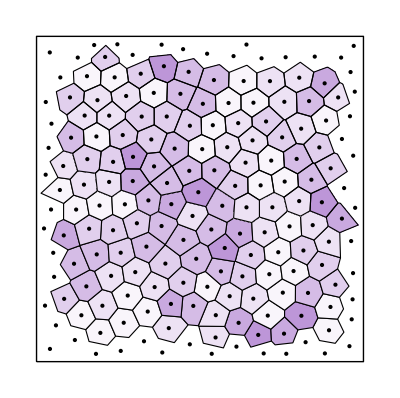
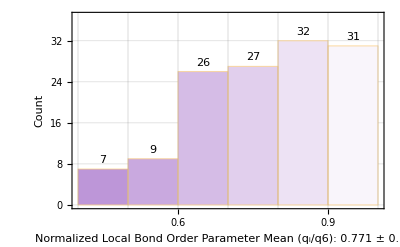

```mathematica
(* Default return of PlotVoronoi Tesselations. Bond Order Parameter used for colouring. This is the type->"bop" option (see below).*)
PlotVoronoiTessellations@xyl200
```

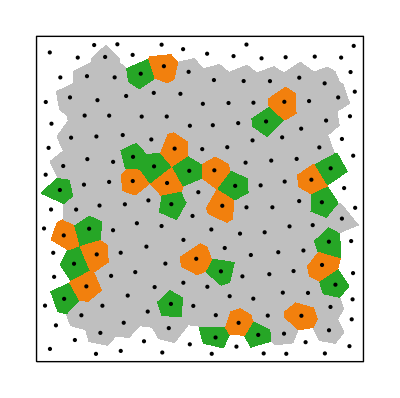
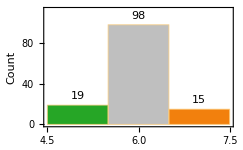

```mathematica
(*Two other colour schemes are available and can be specified using type*)
PlotVoronoiTessellations[xyl200, type->"coord"] (*Voronoi cells coloured by number of sides*)
```

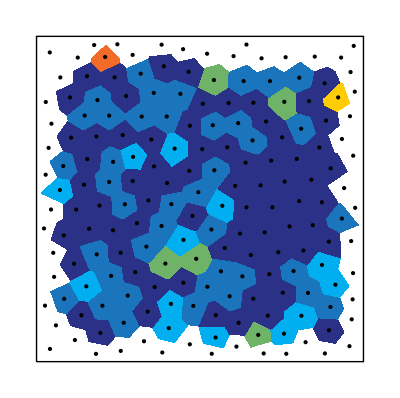
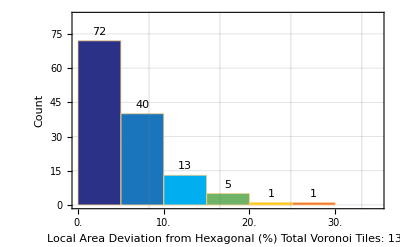

```mathematica
PlotVoronoiTessellations[xyl200, type->"vor"] (*Voronoi cells coloured by area deviation from hexagonal lattice *)
```

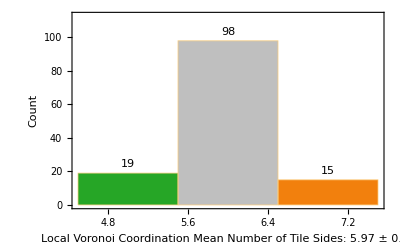
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
(*You can plot all 3 types of tessellation with one command by using the application operators:*)
PlotVoronoiTessellations[xyl200,scalebar->True, type-> #]&/@{"vor","bop","coord"}
```

```mathematica
(*There is also an option to save all of the output files as a png. You can see the saved output in the folder this notebook is saved in.*)
PlotVoronoiTessellations[xyl200, save->True]
```

{-Graphics-,-Graphics-}

```mathematica
(*If you have a .png of the original AFM image of the particle array, you can overlay the voronoi Tessellation with the image as follows *)
myImage = -Graphics- ;(*Yes. You can just copy paste a png*)
(*  Overlay the Nanoparticle Images with the Voronoi Tessellation:  *)
(* a) Image Dimensions tells how many pixels the image is  *)
ImageDimensions[myImage]

(* b) Rescale the points by:  image/box  size  *)
vor=PlotVoronoiTessellations[(410/1000)* xyl200][[1]];

(* c) The double ImageReflect is needed because the jpeg image {0,0} starts at the top left... *)
(*     ...while xy data starts in the bottom left as the origin.  *)
ImageReflect@Show[{ImageReflect[myImage],vor  }]
```

{410,410}

-Graphics-

The PlotVoronoiTessellation function also has options for: 
displaying scalebar, changing image raster, removing points on graphic, changing data truncation type etc. 
For bop type specifically: Changing bin size, setting custom colour gradients etc.
See examples/how to use these options in the documentation file:  "Guide Page: disLocate"paclet:disLocate/guide/disLocate (or find it on our GitHub)
The Documentation also has examples of built in Mathematica functions that could simplify/speed up your disLocate analysis.

### Pair Correlation Function

Documentation: "PlotPairCorrelationFunction"paclet:disLocate/ref/PlotPairCorrelationFunction

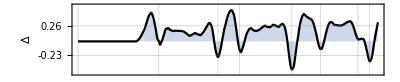
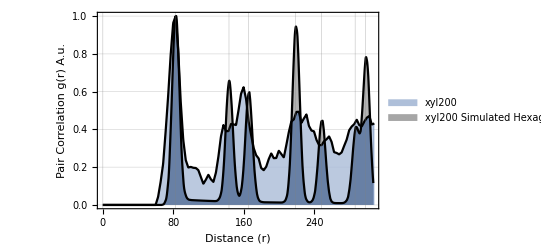
-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
xyl200 | 82.6931 | 82.6236 | 2.5267 | 183 | 187

```mathematica
(*Default output of Pair Correlation Function on single dataset:*)
PlotPairCorrelationFunction@xyl200
```

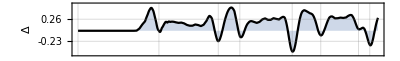
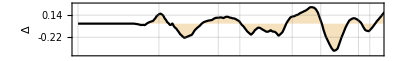
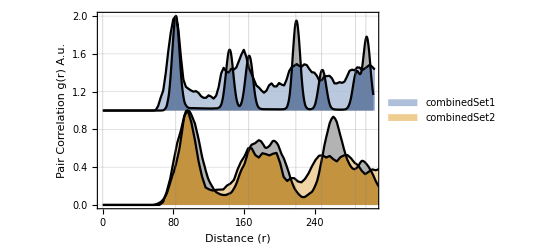
-Graphics-
-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
combinedSet1 | 82.6931 | 82.6236 | 2.5267 | 183 | 187
combinedSet2 | 96.3248 | 97.0426 | 7.45882 | 131 | 136

```mathematica
(*It is possible to plot multiple datasets for comparison, by passing a list of datasets *)
(*Place data in array*)
combinedSet = {xyl200,xyl400};
PlotPairCorrelationFunction@combinedSet
```

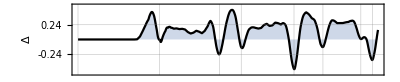
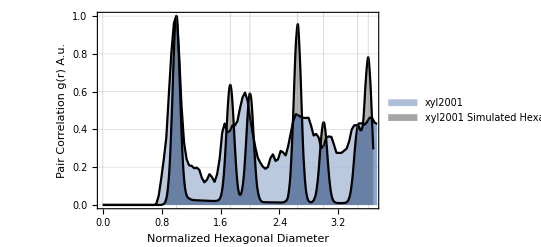
-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
xyl2001 | 82.6931 | 82.6236 | 2.5267 | 183 | 187

```mathematica
(*It is possible to normalize the x-axis to the expected radius of a single particle*)
PlotPairCorrelationFunction[xyl200, normalized->True]
```

The PlotPairCorrelationFunction also has options for:
Unscaling the y axis to be not-normalized, selecting custom colours for each dataset, changing lattice type, changing dataset labels and more. 
Read the documentation here: "PlotPairCorrelationFunction"paclet:disLocate/ref/PlotPairCorrelationFunction for examples.